```mathematica
Quiet[Remove["Global`*"]]
```

```mathematica
Needs["NumericalDifferentialEquationAnalysis`"];
```

## Bilinear Quadrilateral element

```mathematica
PlaneQuad4Element[ type_,e_,nu_,h_,{bx_,by_},{{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_}}]:=
Module[{cMat,sloc,swts,tloc,twts,gpLocs,gpWts,n,s,t,dns,dnt,xst,yst,
J,npt,Jpt, dnsPt, dntPt,detJ,k,r,dnx,dny,BT,B,Npt},

(*Elasticity tensor*)
Switch[type,
PlaneStress,
cMat=e/(1-nu^2){{1,nu,0},{nu,1,0},{0,0,(1-nu)/2}},
PlaneStrain,
cMat=e/((1+nu)(1-2nu)){{1-nu,nu,0},{nu,1-nu,0},{0,0,(1-2nu)/2}}
];

(*Gauss Quadrature*)
{sloc,swts}=Transpose[GaussianQuadratureWeights[2,-1,1]];
{tloc,twts}=Transpose[GaussianQuadratureWeights[2,-1,1]];
gpLocs=Flatten[Outer[List,sloc,tloc],1];
gpWts=Flatten[Outer[Times,swts,twts],1];

(*Bilinear shapefunction - mapping - JacobianMatrix*)
n={
(1/4)*(1-s)*(1-t),
(1/4)*(s+1)*(1-t),
(1/4)*(s+1)*(t+1),
(1/4)*(1-s)*(t+1)
};
{dns,dnt}={D[n,s],D[n,t]};
xst=n.{x1,x2,x3,x4};
yst=n.{y1,y2,y3,y4};
J={{D[xst,s],D[xst,t]},{D[yst,s],D[yst,t]}};

(*initial variables for element K and element r*)
k=Table[0,{8},{8}];
r=Table[0,{8}];

(*Integration*)
Do[
pt={s->gpLocs[[i,1]],t->gpLocs[[i,2]]};
w=gpWts[[i]];
{npt, Jpt, dnsPt, dntPt}={n,J,dns,dnt}/.pt;
Npt=Transpose[{
{npt[[1]],0,npt[[2]],0,npt[[3]],0,npt[[4]],0},
{0,npt[[1]],0,npt[[2]],0,npt[[3]],0,npt[[4]]}
}];
detJ=Det[Jpt];
dnx=(Jpt[[2,2]] dnsPt-Jpt[[2,1]] dntPt)/detJ;
dny=(-Jpt[[1,2]] dnsPt+Jpt[[1,1]] dntPt)/detJ;
B={
{dnx[[1]],0,dnx[[2]],0,dnx[[3]],0,dnx[[4]],0},
{0,dny[[1]],0,dny[[2]],0,dny[[3]],0,dny[[4]]},
{dny[[1]],dnx[[1]],dny[[2]],dnx[[2]],dny[[3]],dnx[[3]],dny[[4]],dnx[[4]]}
};
BT=Transpose[B];
k+=h detJ w BT.cMat.B;
r+=h detJ w Npt.{bx,by},
{i,1,Length[gpWts]}
];

{k,r}
]
```

```mathematica
PlaneQuad4Load[side_,qn_,qt_,h_,{{x1_, y1_}, {x2_,y2_},{x3_,y3_},{x4_,y4_}}]:=Module[{r,pts,wts,n,s,t,a,xa,ya,Jc,Jcpt, nx, ny, qx, qy,Npt},
r=Table[0,{8}];
{pts,wts}=Transpose[GaussianQuadratureWeights[2,-1,1]];
n={
(1/4)*(1-s)*(1-t),
(1/4)*(s+1)*(1-t),
(1/4)*(s+1)*(t+1),
(1/4)*(1-s)*(t+1)
};
n=Switch[side,
1,n/.{s->a,t->-1},
2, n/.{s->1,t->a},
3, n/.{s->-a,t->1},
4, n/.{s->-1,t->-a}
];
xa=n.{x1,x2,x3,x4};
ya=n.{y1,y2,y3,y4};
Jc=Sqrt[D[xa,a]^2+D[ya,a]^2];
nx=D[ya,a]/Jc;ny=-D[xa,a]/Jc;
qx=nx qn-ny qt;
qy=ny qn+nx qt;
Do[{npt, Jcpt}={n,Jc}/.a->pts[[i]];
Npt=Transpose[{{npt[[1]],0,npt[[2]],0,npt[[3]],0,npt[[4]],0},
{0,npt[[1]],0,npt[[2]],0,npt[[3]],0,npt[[4]]}}];
r+=h *Jcpt * wts[[i]]  Npt.{qx,qy},
{i,1,Length[pts]}
];
r
];
```

```mathematica
PlaneQuad4Results[ type_,e_,nu_,{{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_}},d_]:=Module[{pt,n,dns,dnt,bx,by,xst,yst,J,npt, Jpt, dnsPt, dntPt,detJ,loc,cMat,s,t,dnx,dny,B,Npt,eps,sx,sy,sxy},

pt={s->0,t->0}; (*Calculate stress & strain at center of reference element*)

(*Elasticity tensor*)
Switch[type,
PlaneStress,
cMat=e/(1-nu^2){{1,nu,0},{nu,1,0},{0,0,(1-nu)/2}},
PlaneStrain,
cMat=e/((1+nu)(1-2nu)){{1-nu,nu,0},{nu,1-nu,0},{0,0,(1-2nu)/2}}
];
(*Bilinear shapefunction - mapping - JacobianMatrix*)
n={
(1/4)*(1-s)*(1-t),
(1/4)*(s+1)*(1-t),
(1/4)*(s+1)*(t+1),
(1/4)*(1-s)*(t+1)
};
{dns,dnt}={D[n,s],D[n,t]};
xst=n.{x1,x2,x3,x4};
yst=n.{y1,y2,y3,y4};
J={{D[xst,s],D[xst,t]},{D[yst,s],D[yst,t]}};
{loc,npt, Jpt, dnsPt, dntPt}={{xst,yst},n,J,dns,dnt}/.pt;
detJ=Det[Jpt];

dnx=(Jpt[[2,2]] dnsPt-Jpt[[2,1]] dntPt)/detJ;
dny=(-Jpt[[1,2]] dnsPt+Jpt[[1,1]] dntPt)/detJ;
Npt=Transpose[{{npt[[1]],0,npt[[2]],0,npt[[3]],0,npt[[4]],0},
{0,npt[[1]],0,npt[[2]],0,npt[[3]],0,npt[[4]]}}];
B={{dnx[[1]],0,dnx[[2]],0,dnx[[3]],0,dnx[[4]],0},
{0,dny[[1]],0,dny[[2]],0,dny[[3]],0,dny[[4]]},
{dny[[1]],dnx[[1]],dny[[2]],dnx[[2]],dny[[3]],dnx[[3]],dny[[4]],dnx[[4]]}};

(*Strain vector*)
eps=B.d;
(*Stress vector*)
{sx,sy,sxy}=cMat.eps;

(*Outputs*)
{loc,eps, {sx,sy,sxy},Eigenvalues[{{sx,sxy},{sxy,sy}}],Sqrt[(sx-sy)^2+sy^2+sx^2+6 sxy^2]/Sqrt[2]}
]
```

## Test

```mathematica
e=3000*10^3; nu=0.2; h=4; q=50;
nodes={{0,5},{0,12},{6,0},{6,5},{20,0},{20,12},{54,0},{54,12}};

en[1]={1,4,6,2};lm[1]={1,2,7,8,11,12,3,4};
en[2]={3,5,6,4};lm[2]={5,6,9,10,11,12,7,8};
en[3]={5,7,8,6} ; lm[3]={9,10,13,14,15,16,11,12};
```

#### Element stiffness and forces

```mathematica
{k[1],r[1]}=PlaneQuad4Element[PlaneStress,e,nu,h,{0,0},nodes[[en[1]]]];
{k[2],r[2]}=PlaneQuad4Element[PlaneStress,e,nu,h,{0,0},nodes[[en[2]]]];
{k[3],r[3]}=PlaneQuad4Element[PlaneStress,e,nu,h,{0,0},nodes[[en[3]]]];
```

#### Impose distributed loads

```mathematica
r[1]+=PlaneQuad4Load[3,-q,0,h,nodes[[en[1]]]]
r[3]+=PlaneQuad4Load[3,-q,0,h,nodes[[en[3]]]]
```

{0.,0.,0.,0.,0.,-2000.,0.,-2000.}

{0.,0.,0.,0.,0.,-3400.,0.,-3400.}

#### Assembly global stiffness and global force

```mathematica
K=Table[0,{16},{16}];R=Table[0,{16}];
Do[K[[lm[i],lm[i]]]+=k[i];
R[[lm[i]]]+=r[i],{i,1,3}];
```

```mathematica
K//MatrixForm;
```

LinearSolve::npdef: The matrix {{6.26209×10^6,-16375.5,-1.19113×10^6,-120087.,0.,0.,-4.11923×10^6,1.26638×10^6,0.,0.,«6»},{-16375.5,9.0354×10^6,-1.37009×10^6,-5.58562×10^6,0.,0.,2.51638×10^6,-3.67826×10^6,0.,0.,«6»},«7»,{0.,0.,0.,0.,-1.17054×10^6,2.74625×10^6,2.42054×10^6,-4.8891×10^6,-866443.,1.97912×10^7,«6»},«6»} is not positive definite.

LinearSolve[{{6.26209×10^6,-16375.5,-1.19113×10^6,-120087.,0,0,-4.11923×10^6,1.26638×10^6,0,0,-951731.,-1.12991×10^6,0,0,0,0},{-16375.5,9.0354×10^6,-1.37009×10^6,-5.58562×10^6,0,0,2.51638×10^6,-3.67826×10^6,0,0,-1.12991×10^6,228478.,0,0,0,0},{-1.19113×10^6,-1.37009×10^6,7.54484×10^6,-2.96397×10^6,0,0,-5.95173×10^6,2.62009×10^6,0,0,-401981.,1.71397×10^6,0,0,0,0},{-120087.,-5.58562×10^6,-2.96397×10^6,1.50507×10^7,0,0,2.62009×10^6,-1.22715×10^7,0,0,463974.,2.80646×10^6,0,0,0,0},{0,0,0,0,5.7276×10^6,559291.,-3.49546×10^6,1.94071×10^6,-771918.,-1.17054×10^6,-1.46023×10^6,-1.32946×10^6,0,0,0,0},{0,0,0,0,559291.,9.65901×10^6,690709.,-8.76615×10^6,79462.1,2.74625×10^6,-1.32946×10^6,-3.6391×10^6,0,0,0,0},{-4.11923×10^6,2.51638×10^6,-5.95173×10^6,2.62009×10^6,-3.49546×10^6,690709.,2.01147×10^7,-6.95708×10^6,-4.58523×10^6,2.42054×10^6,-1.96304×10^6,-1.29063×10^6,0,0,0,0},{1.26638×10^6,-3.67826×10^6,2.62009×10^6,-1.22715×10^7,1.94071×10^6,-8.76615×10^6,-6.95708×10^6,3.24444×10^7,2.42054×10^6,-4.8891×10^6,-1.29063×10^6,-2.83938×10^6,0,0,0,0},{0,0,0,0,-771918.,79462.1,-4.58523×10^6,2.42054×10^6,1.25561×10^7,-866443.,-4.99308×10^6,866443.,890523.,-625000.,-3.09641×10^6,-1.875×10^6},{0,0,0,0,-1.17054×10^6,2.74625×10^6,2.42054×10^6,-4.8891×10^6,-866443.,1.97912×10^7,866443.,-1.6766×10^7,625000.,5.31454×10^6,-1.875×10^6,-6.1969×10^6},{-951731.,-1.12991×10^6,-401981.,463974.,-1.46023×10^6,-1.32946×10^6,-1.96304×10^6,-1.29063×10^6,-4.99308×10^6,866443.,1.19759×10^7,-80416.3,-3.09641×10^6,1.875×10^6,890523.,625000.},{-1.12991×10^6,228478.,1.71397×10^6,2.80646×10^6,-1.32946×10^6,-3.6391×10^6,-1.29063×10^6,-2.83938×10^6,866443.,-1.6766×10^7,-80416.3,2.10919×10^7,1.875×10^6,-6.1969×10^6,-625000.,5.31454×10^6},{0,0,0,0,0,0,0,0,890523.,625000.,-3.09641×10^6,1.875×10^6,6.19281×10^6,-1.875×10^6,-3.98693×10^6,-625000.},{0,0,0,0,0,0,0,0,-625000.,5.31454×10^6,1.875×10^6,-6.1969×10^6,-1.875×10^6,1.23938×10^7,625000.,-1.15114×10^7},{0,0,0,0,0,0,0,0,-3.09641×10^6,-1.875×10^6,890523.,-625000.,-3.98693×10^6,625000.,6.19281×10^6,1.875×10^6},{0,0,0,0,0,0,0,0,-1.875×10^6,-6.1969×10^6,625000.,5.31454×10^6,-625000.,-1.15114×10^7,1.875×10^6,1.23938×10^7}},{0.,0.,0.,-2000.,0.,0.,0.,0.,0.,0.,0.,-5400.,0.,0.,0.,-3400.},Method→Cholesky]

#### Impose Dirichlet BC

```mathematica
debc={1,3,13,14,15,16};         (*fixed DOFs*)
ebcVals=Table[0,{6}];                   (*fixed values*)
df = Complement[Range[16],debc](*free DOFs*)
```

{2,4,5,6,7,8,9,10,11,12}

```mathematica
Kf=K[[df,df]];
%//MatrixForm
```

(9.0354×10^6 | -5.58562×10^6 | 0 | 0 | 2.51638×10^6 | -3.67826×10^6 | 0 | 0 | -1.12991×10^6 | 228478.
-5.58562×10^6 | 1.50507×10^7 | 0 | 0 | 2.62009×10^6 | -1.22715×10^7 | 0 | 0 | 463974. | 2.80646×10^6
0 | 0 | 5.7276×10^6 | 559291. | -3.49546×10^6 | 1.94071×10^6 | -771918. | -1.17054×10^6 | -1.46023×10^6 | -1.32946×10^6
0 | 0 | 559291. | 9.65901×10^6 | 690709. | -8.76615×10^6 | 79462.1 | 2.74625×10^6 | -1.32946×10^6 | -3.6391×10^6
2.51638×10^6 | 2.62009×10^6 | -3.49546×10^6 | 690709. | 2.01147×10^7 | -6.95708×10^6 | -4.58523×10^6 | 2.42054×10^6 | -1.96304×10^6 | -1.29063×10^6
-3.67826×10^6 | -1.22715×10^7 | 1.94071×10^6 | -8.76615×10^6 | -6.95708×10^6 | 3.24444×10^7 | 2.42054×10^6 | -4.8891×10^6 | -1.29063×10^6 | -2.83938×10^6
0 | 0 | -771918. | 79462.1 | -4.58523×10^6 | 2.42054×10^6 | 1.25561×10^7 | -866443. | -4.99308×10^6 | 866443.
0 | 0 | -1.17054×10^6 | 2.74625×10^6 | 2.42054×10^6 | -4.8891×10^6 | -866443. | 1.97912×10^7 | 866443. | -1.6766×10^7
-1.12991×10^6 | 463974. | -1.46023×10^6 | -1.32946×10^6 | -1.96304×10^6 | -1.29063×10^6 | -4.99308×10^6 | 866443. | 1.19759×10^7 | -80416.3
228478. | 2.80646×10^6 | -1.32946×10^6 | -3.6391×10^6 | -1.29063×10^6 | -2.83938×10^6 | 866443. | -1.6766×10^7 | -80416.3 | 2.10919×10^7)

```mathematica
Rf=R[[df]]-K[[df,debc]].ebcVals (*impose eBC values*)
```

{0.,-2000.,0.,0.,0.,0.,0.,0.,0.,-5400.}

#### Nodal solutions

```mathematica
dfVals=LinearSolve[Kf,Rf] (*only nodal solutions at free DOFs*)
```

{-0.0183155,-0.0183204,0.00275915,-0.0166486,0.00114552,-0.0164634,0.00305003,-0.0113566,-0.00210128,-0.0116254}

```mathematica
d=Table[0,{16}];
d[[debc]]=ebcVals;
d[[df]]=dfVals;
d (*complete nodal solutions*)
```

{0,-0.0183155,0,-0.0183204,0.00275915,-0.0166486,0.00114552,-0.0164634,0.00305003,-0.0113566,-0.00210128,-0.0116254,0,0,0,0}

#### Outputs: {centerPts, strain Vect, Stress Vect, Principal stresses, von Mises}

```mathematica
PlaneQuad4Results[ PlaneStress,
e,nu,
nodes[[en[1]]], (*Element 1*)
d[[lm[1]]]             (*Displacement of Element 1*)
]
```

{{13/2,17/2},{-0.00003676,0.0000164861,0.000133582},{-104.571,28.544,166.978},{-217.768,141.741},313.656}

```mathematica
PlaneQuad4Results[ PlaneStress,
e,nu,
nodes[[en[2]]], (*Element 2*)
d[[lm[2]]]             (*Displacement of Element 2*)
]
```

{{13,17/4},{-6.08383×10^-6,-4.91655×10^-6,-0.0000349244},{-22.0848,-19.1666,-43.6555},{-64.3056,23.0542},78.4169}

```mathematica
PlaneQuad4Results[ PlaneStress,
e,nu,
nodes[[en[3]]], (*Element 3*)
d[[lm[3]]]             (*Displacement of Element 3*)
]
```

{{37,6},{-0.0000139523,-0.000011199,0.000123333},{-50.6003,-43.7172,154.167},{-201.364,107.046},271.222}

#### Visualization

```mathematica
u =100*d; (*scale factor = 100*)
NewNodes=Table[{nodes⟦i,1⟧+u⟦2i-1⟧,nodes⟦i,2⟧+u⟦2i⟧},{i,1,Length[nodes]}];
```

Ux displacement:

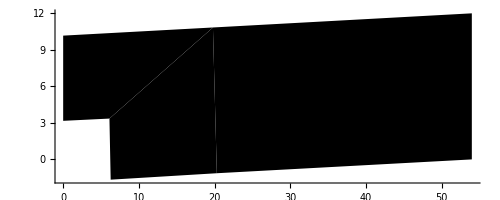

```mathematica
Show[Graphics[
Polygon[
NewNodes[[en[1]]],VertexColors->Hue/@u[[lm[1]]][[;;;;2]]],Axes->True],
Graphics[
Polygon[
NewNodes[[en[2]]],VertexColors->Hue/@u[[lm[2]]][[;;;;2]]],Axes->True],
Graphics[
Polygon[
NewNodes[[en[3]]],VertexColors->Hue/@u[[lm[3]]][[;;;;2]]],Axes->True]
]
```

Uy displacement:

```mathematica
Show[Graphics[
Polygon[
NewNodes[[en[1]]],VertexColors->Hue/@u[[lm[1]]][[2;;;;2]]],Axes->True],
Graphics[
Polygon[
NewNodes[[en[2]]],VertexColors->Hue/@u[[lm[2]]][[2;;;;2]]],Axes->True],
Graphics[
Polygon[
NewNodes[[en[3]]],VertexColors->Hue/@u[[lm[3]]][[2;;;;2]]],Axes->True]
]
```

-Graphics-